```mathematica
<<VectorFieldPlots`;
```

General::obspkg: VectorFieldPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
(*define the slope*)
```

```mathematica
svl=γ/2-1/2 l(-3γ l - f);
svf=-1/2-1/2 f(-3γ l - f);
```

```mathematica
γ=0;
```

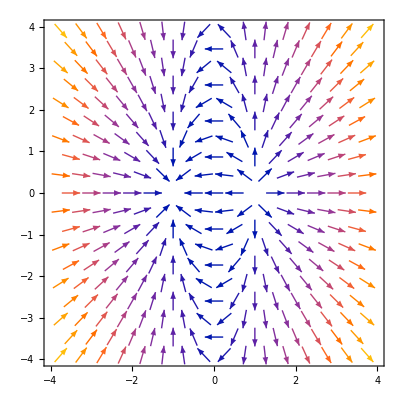

```mathematica
field=VectorPlot[{svf,svl},{f,-4,4},{l,-4,4},VectorStyle->Arrowheads[0.025]]
```

```mathematica
(*this is figure 5 from scott's paper, huge*)
```

```mathematica
line1=ParametricPlot[{1,t},{t,-4,4},PlotStyle->{Dashed,Thick}];
line2=ParametricPlot[{-1,t},{t,-4,4},PlotStyle->{Dashed,Thick}];
(*hamiltonian constraint in both quadrants*)
q1=Plot[y=√((-(1-x^2))/3),{x,-4,4},PlotStyle->Directive[Darker[Green,1],Thick]];
q2=Plot[y=-√((-(1-x^2))/3),{x,-4,4},PlotStyle->Directive[Darker[Green,1],Thick]];
q3=Plot[y=√((-(1+x^2))/3),{x,-4,4},PlotStyle->Directive[Darker[Green,1],Thick]];
q4=Plot[y=-√((-(1+x^2))/3),{x,-4,4},PlotStyle->Directive[Darker[Green,1],Thick]];
```

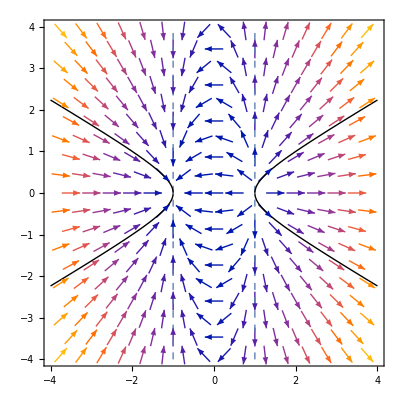

```mathematica
Show[field,line1,line2,q1,q2,q3,q4]
```

```mathematica
Clear[l,f]
```

```mathematica
eq1=l'[t]==γ/2-1/2 l[t](-3γ l[t] - f[t]);
eq2=f'[t]==-1/2-1/2 f[t](-3γ l[t] - f[t]);
sol=NDSolve[{eq1,eq2,l[0]==3,f[0]==0.5},{l,f},{t,0,10000}]
```

{{l→InterpolatingFunction[…],f→InterpolatingFunction[…]}}

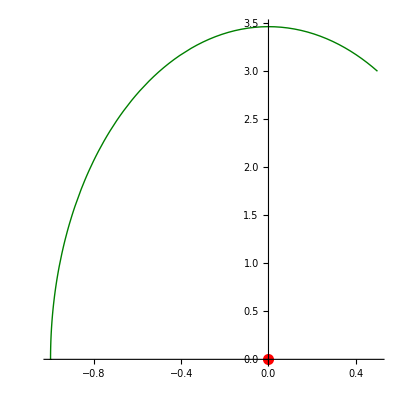

```mathematica
phase1=ParametricPlot[Evaluate[{f[x],l[x]}/.sol],{x,0,200},PlotStyle->Directive[Darker[Green,0.5],Thick],Epilog->{PointSize[0.02],Red,Point[{0,0}]},AspectRatio->1,PlotRange->All]
```

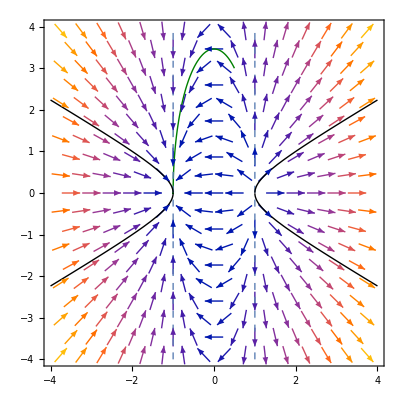

```mathematica
Show[field,phase1,line1,line2,q1,q2,q3,q4]
```